# Numerical Solutions to the Schrödinger Equation

Richard Gass
Department of Physics, University of Cincinnati
Cincinnati, OH 45221-0011
gass@physics.uc.edu

##### Last Revision May 27, 2008

## Initialization

```mathematica
<<Notation`;
<<PlotLegends`;
```

```mathematica
Developer`SetSystemOptions["EvaluateNumericalFunctionArgument"->False];
Symbolize[a_+]
Symbolize[Subscript[a, _]]
Symbolize[Subscript[α, 1]]
Symbolize[Subscript[α, 2]]
Symbolize[Subscript[β, 2]]
Symbolize[Subscript[k, 0]]
Symbolize[Subscript[σ, 0]]
Symbolize[Subscript[x, 0]]
```

```mathematica
SubPlus[a][f_]:=Simplify[-D[f,q]+q  f]
SubMinus[a][f_]:=Simplify[D[f,q]+q  f]
ψ0=(1/√π)^(1/2)Exp[-q^2/2];
ψ[n_,q_]:=Nest[SubPlus[a],ψ0,n]/Product[√(2(i+1)),{i,0,n-1}]
```

#### Note to the student

All the exercises in this notebook call for written responses not just code. You should clearly explain what you are doing, why you are doing it and why you believe (or don't believe) your results.  You should discuss what your results mean and if appropriate what further lines of investigation might be fruitful.

##### What to do if the code does not work

This notebook is designed to run with Mathematica 6.0 to 7.01 . The code will probably work in higher versions of Mathematica, but large portions of the code will not work in version 5.2. If the code does not work in versions 6.0 or 7.01 the problem is almost certainly one of two things: 1) you forgot to run a line of code earlier in the notebook or 2) you used a variable or a name that is used for another propose in the notebook, and you now have a naming conflict.

#### Note to the instructor

I have tried to arrange the material in this notebook so that it can be used in a flexible manner.  If you are short on time you can stop at the end of the section on eigenvalue problems. If you do this, the material can be covered in two weeks or less. But you will need to come up with a project for the students since both suggested projects involve the time-dependent behavior of wave packets. One possibility is to combine problems three and four into a project. The sections on wave packet splitting and charge oscillation are independent and depending on time and interest you may cover one or both.

#### Prerequisites

##### Software

Students should have a basic familiarity with Mathematica. They do not need to be Mathematica experts but they do need to know how to run code, make simple plots and understand the basics of Mathematica syntax.

##### Mathematics

The minimum mathematics prerequisite is a full year of calculus and an understanding of what a differential equation is and what an initial value problem is. Students should also have been exposed to the concept of an eigenvalue problem. Ideally students will have had or be currently enrolled in a course in differential equations.

##### Physics

The minimum physics prerequisite is a full year of calculus-based physics with a co-requisite of modern physics or an introductory quantum mechanics course. In particular, students need to have seen the Schrödinger equation before. If they have not the instructor will have to introduce the Schrödinger equation.

#### Module Objectives

After completion of this module students should:

•	Understand how to solve an initial value problem numerically.

•	Understand the difference between an initial value problem and a boundary value problem.

•	Understand how to solve an boundary value problem numerically.

•	Understand how to solve an eigenvalue problem numerically.

•	Understand how to implement the method of lines.

•	Understand how to check the accuracy of their solutions.

•	Have developed a better intuition about wave functions and time dependent quantum phenomena.

•	Have been exposed to topics in wave packet dynamics that are of current research interest.

#### Competencies covered in this notebook

Modeling

1.3 Create a conceptual model 
1.4 Examine various mathematical representations of functions
1.5 Analyze issues in accuracy and precision
1.7 Demonstrate computational programming utilizing a higher level language

Programming and Algorithms

3.1 Describe the solution methodology for first-order linear differential and difference equations

Numerical Methods

4.4 Analyze techniques for computing eigenvalues-eigenvectors 
4.6 Describe numerical methods for Ordinary Differential Equations
4.7 Describe numerical methods for Partial Differential Equations

## Introduction

Studying quantum mechanics in one-dimension  allows you to learn the basics of quantum mechanics and to develop your quantum intuition without some of the mathematical complexities present in three-dimensions. In the old days (before 1974) one- dimensional quantum mechanics problems were  just textbook problems, without real world applications. However in 1974 Dingle, Wiegmann and Henry at Bell Labs made a particle in a box [1]. Now experiments on one-dimensional quantum systems are common place. One-dimensional quantum systems lie at the heart of semiconductor devices such as quantum-well lasers [2]. In this module the methods needed for the numerical solution of the Schrödinger equation are developed, and then used to model realistic semiconductor devices.  We will also be interested in modeling the dynamics of wave packets in quantum wells since this is an area of great interest experimentally.

## The Schrödinger Equation

We will very briefly review the Schrödinger equation. If you are completely unfamiliar with the Schrödinger equation you should consult a textbook on modern physics such as Thornton and Rex [3] or an introductory book on quantum mechanics such as Phillips [4].  Quantum mechanics tells us that particles have wave-like behavior and the  Schrödinger equation is the wave equation which describes this behavior.

### The time-dependent case

The one-dimensional Schrödinger equation for a particle in a time-independent potential is

(-  ℏ^2)/(2 m)(∂^2 Ψ(x,t))/(∂x^2)+V(x) Ψ(x,t)=ⅈ ℏ(∂Ψ(x,t))/(∂t) ,

where m is the mass of the particle, V(x) is the potential that the particle moves in, and Ψ(x,t) is the particle's wave function. The physical interpretation of the wave function is that Ψ^*(x,t) Ψ(x,t) ⅆx is the probability of finding the particle between x and x+ ⅆx. The notation Ψ^* denotes taking the complex conjugate which means that everywhere an ⅈ appears in Ψ you replace it by -ⅈ. For example if Ψ(x,t)=ⅇ^(ⅈ(k x -ω t))  then Ψ^*(x,t)=ⅇ^(-ⅈ(k x -ω t)) .  In general the wave function Ψ will be complex, not real.

For bound state problems we generally require that the wave function be normalized, which is to say that ∫ Ψ^*(x,t) Ψ(x,t) ⅆx=1 where the integral runs over all possible values of x. This condition simply means that if we look everywhere, we find the particle once and only once.

In quantum mechanics a particle does not have a definite position (at least not until we measure the particles position) but only has a probability of being found at a position. If we have a million hydrogen atoms all in the ground state and we measure the position of the electron in all million atoms, we will get a different answer for each atom. It does not make sense to talk about a definite position in a quantum system but only an average position. Since  Ψ^*(x,t) Ψ(x,t) is the probability distribution, the average position of a particle is <x>=∫Ψ^*(x,t) x Ψ(x,t)ⅆx. In quantum mechanics angular brackets are used to denote an average. In general, the average or expectation value of an observable 𝒪 is <𝒪>=∫Ψ^*𝒪Ψ ⅆx and order matters! You can not interchange the operator 𝒪 and Ψ^* or Ψ except in special cases.

### The time-independent case

If the potential is time independent we can separate the time-dependent Schrödinger equation into a spacial part and a temporal part. We look for a solution of the form Ψ(x,t)=ψ(x) T(t). Substituting this into equation (0.1) gives

-ℏ^2/(2m)(1/ψ(x))(ⅆ^2 ψ(x))/(ⅆ x^2)+V(x) =(ⅈ ℏ)/(T(t)) (ⅆT(t))/ⅆt .

Since the left-hand side depends only on x and the right-hand side depends only on t, each side must be equal to a constant which we will call E. This gives

-ℏ^2/(2m)(ⅆ^2 ψ(x))/(ⅆ x^2)+V(x) ψ(x)=E ψ(x)

and

(ⅆT(t))/ⅆt=(-ⅈ/ℏ) E T(t)  .

Equation (0.4) is solved by T(t)= A ⅇ^(-ⅈ E t/ℏ) and equation three is the time-independent Schrödinger equation.  In general, equation (0.3) cannot be satisfied for arbitrary values of E but only for certain particular values of E. These values are known as the eigenvalues of the operator -ℏ^2/(2m) ⅆ^2/(ⅆ x^2)+V(x) and are the allowed energies. The associated wave functions are known as the eigenfunctions.

#### Particle in a box

This is best illustrated with an example. The simplest case is a particle in a one-dimensional box or infinite well of length L. The potential is 
V(x) = { ∞ | x<0
0 | 0<x<L
∞ | x>L and is shown below in figure 1.

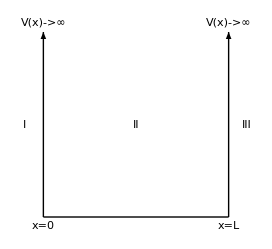

Figure1: An infinite potential well. The wave function must vanish in regions I and III and thus must vanish at the well boundaries..

In region II the time-independent Schrödinger equation is 
-ℏ^2/(2m)(ⅆ^2 ψ(x))/(ⅆ x^2)=E ψ(x)  which we can write as (ⅆ^2 ψ(x))/(ⅆ x^2)+k^2 ψ(x)=0 where k^2=2m E/ℏ^2. Note that k has units of inverse length and is a wave-number. This is just the equation for a harmonic oscillator and thus has solutions ψ(x)=A  cos(k x)+B sin(k x). We need ψ(0)=0 ⇒A=0.  At the right boundary ψ(L)=0 ⇒ sin(k L)=0. Thus, k= n π/L  where n is a positive integer. Therefore E= k^2 ℏ^2/(2m)=n^2 ℏ^2 π^2/(2m L^2). Notice that it is the boundary conditions that give rise to the quantization of the energy levels. The remaining constant B is fixed by the normalization condition ∫_0^L ψ^*ψⅆx=1 ⇒B^2∫_0^L sin^2(n π x/L)ⅆx=1 ⇒B=√(2/L).

In practice we will be interested not in infinite wells, but in finite wells such as the well shown in Figure 2. The potential for a finite well is V(x) = { 0 | x<0
-V_0 | 0<x<L
0 | x>L where V_0>0.

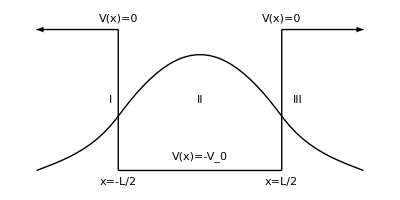

Figure 2: A finite well of depth V_0 and the ground state wave function. For a finite well there is a non-zero probability that the particle will be found outside the well. Since the ground state has an energy that is less then zero the particle would be classically forbidden in regions I and III. The wave function always falls off exponentially in classically forbidden regions.

#### How do you make a quantum well?

The quantum well studied by Dingle, Wiegmann and Henry was made by sandwiching a thin (on the order of 10-50 nanometers) layer of Gallium-Arsenic (GaAs) between two thick layers of Aluminum-Gallium-Arsenic (AlGaAs). This results in a quasi-one-dimensional well.  Such wells are called quasi-one- dimensional because the charge carriers which could be electrons and or holes are free to move to the plane of the GaAs layer but are confined at the boundaries provided by the AlGaAs slabs. The physics of how the height of the well depends on the composition of the semiconductor is somewhat involved and would take us to far afield. Interested readers should consult Bastard [5] or Weisburch and Vinter[2].

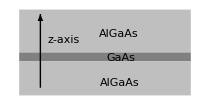
-Graphics- |

Figure 3:  Schematic drawing of a single quantum well.  Electrons and holes are free to move in the x and y directions but are confined in the  z direction.

-Graphics-

Figure 4: An image taken with a scanning tunneling microscope (STM) of a slice of a In_0.2 Ga_0.8 As/GaAs multiple quantum well structure. Image is from Nikos Jäger's web page.

One way to make a quantum well in the lab is to use molecular beam epitaxy or MBE.  You can think of an MBE machine as a very high-tech and expensive paint sprayer. An MBE machine allows you to sputter materials onto a substrate in a vacuum. As a result you have good control over both the composition and thickness of the layers. A more detailed but accessible account of molecular beam epitaxy can be found in Ibach and Lüth [6].  If you lay down multiple thin layers of GaAs separated by thin layers of AlGaAs you can make multiple quantum wells. By varying the composition you can vary the depth of the wells. One can also make barriers. Although AlGaAs/GaAs is a popular choice, one can use other semiconductors. The well structure shown in figure 4 uses InGaAs/GaAs.

| -Graphics--Graphics-

Figure 5: The left figure is a schematic of an MBE machine.Figure from http://users.rcn.com/qsa/waveeng.html.  On the right is a picture of Professor Andrew Steckel's MBE machine at the University of Cincinnati. Photograph is from http://www.nanolab.uc.edu/.

## Numerical Solutions of Initial Value Problems

Before we can understand how to find the eigenvalues of an operator numerically, we must first understand how to solve an initial value problem numerically.

### The Euler method

Suppose we have a differential equation of the form dy(x)/dx=f(x). If we replace dy/dx by (y[x_(i+1)]-y[x_i])/(x_(i+1)-x_i) then we can write y[x_(i+1)]= (x_(i+1)-x_i) f(x_i)+y[x_i]. This is the simplest method for numerical solution of a differential equation and is known as Euler's method.

```mathematica
Clear[Euler]
	Euler::usage="Euler[f,y,y0,{t,tmin,tmax},n]  solves the differential equation 
		dy/dt =f subject to the initial condition y[0]=y0 over the interval [tmin,tmax] using n steps and plots solution.The default value of n is 20.";
			
			Euler[f_,y_,y0_,{t_,tmin_,tmax_},n_:20]:=Module[{h,ydata,tdata,data},
		h=N[(tmax-tmin)/n];
		y[1]=y0;
		ydata=Join[{y[1]},Table[y[i+1]=y[i]+h f/.t->i,{i,1,n}]];
		tdata=Table[t,{t,tmin,tmax,h}];
		data=Transpose[{tdata,ydata}];
		ListPlot[data]]
```

Here the Euler method is called on the equation dy(t)/dt =(1-y(t))^2 with y(0)=0. Twenty steps are taken over the interval zero to one.

```mathematica
plot1=Euler[(1-y[t])^2,y,0,{t,0,1.}]
```

Here we take one hundred steps.

```mathematica
plot2=Euler[(1-y[t])^2,y,0,{t,0,1.},100]
```

Our test equation is easy to solve exactly, so we can check the accuracy of our method.

```mathematica
eqn=D[y[t],t]==(1-y[t])^2
```

```mathematica
Clear[y]
result=	First[DSolve[{eqn,y[0]==0},y[t],t]]
```

```mathematica
plot3=Plot[y[t]/.result,{t,0,1},PlotStyle->RGBColor[1,0,0]]
```

Comparing the exact solution (in red) with the numerical approximation shows that the method is not very accurate unless we take many steps.

```mathematica
Show[plot1,plot3]
```

```mathematica
Show[plot2,plot3]
```

We can use Manipulate to explore how the accuracy for the solution depends on the number of points that we use.

```mathematica
Manipulate[Euler[(1-y[t])^2,y,0,{t,0,1.},n],{n,10,100,10},SaveDefinitions->True]
```

##### Exercise One

Use the Euler method to solve the simple harmonic oscillator (ⅆ^2 x(t))/(ⅆ t^2)+ω^2 x(t)=0. Make a parametric plot of x versus v for several different step sizes. Comment on your result.

You should have noticed that convergence is slow (we need many steps) in the Euler method. We can do better by using a method that is higher order in h.

### Runge-Kutta methods

Once again consider dy/dt=f(y,t) Now Taylor expand y(t)  about τ=t+h. I will illustrate this by expanding to second order, but higher order expansions are common.

```mathematica
Clear[h];
equation1=Simplify[Normal[Series[y[t+h],{h,0,2}]]]
```

Since y' = f and y'' = ⅆf(y,t)/ⅆt = ∂f/∂t +(∂y/∂t) ( ∂f/∂y) we have

y(t+h)=y(t)+h f(y,t)+(h^2/2)(∂f/∂t +(∂y/∂t) ( ∂f/∂y))

We can also formally write

y(t+h)=y(t)+α_1 k_1+α_2 k_2 with k_1=h f(y,t)  and k_2= h f(y+β_2 k_1,t+β_1 h)

where the α's and β's are parameters to be determined by comparing equations (0.5) and (0.6) term by term. Doing this gives α_1+α_2=1 and α_2 β_1=α_2 β_2=1/2. Any choice for the α's and β's that satisfies these equations will work. These methods are known as Runge-Kutta methods [7]. We can see exactly how works by expanding eq(0.6).

```mathematica
equation2=y[t]+h Subscript[α, 1] f[t,y[t]] +Subscript[α, 2] h Series[f[t+h Subscript[β, 1],y[t]+Subscript[β, 2] h f[t,y[t]]],{h,0,2}]
```

and using LogicalExpand to equate eq(1) and eq(2) term by term.

```mathematica
result=LogicalExpand[equation1==equation2]
```

Keeping in mind that y'=f(t,y) we see from the order h^0(first) equation that α_1+α_2=1. To solve the order h (second) equation remember that  y'' =ⅆf(y,t)/ⅆt = ∂f/∂t +(∂y/∂t) ( ∂f/∂y). We can use a replacement rule to make this substitution.

```mathematica
result/.D[y[t],{t,2}]->D[f[t,y],t]+D[y[t],t]D[f[t,y],y]
```

Looking at the order h equation we see that 1/2-α_2 β_1=0 and 1/2-α_2 β_2=0 as claimed.

In practice one commonly uses a fourth-order Runge-Kutta method with y(t+h)=y(t)+(1/6)(k_1+2 k_2+2 k_3+k_4)where

 k_1= h f(y,t)
k_2=h f(y+k_1/2,t+h/2)
k_3=h f(y+k_2/2,t+h/2)
k_4 =h f(y+k_3,t+h)

A simple fourth-order Runge-Kutta solver is implemented by the code below which is taken from Maeder[8].

```mathematica
RKStep::usage="RKStep[{f,y,y0,h]  uses a fourth order Runge-Kutta method to take a  single Runge-Kutta step of size h";RKStep[f_,y_,y0_,h_]:=Module[{},
k1=N[h f/.{y->y0}];
k2=N[h f/.{y->y0+k1/2}];
k3=N[h f/.{y->y0+k2/2}];
k4=N[h f/.{y->y0+k3}];
y0+(1 /6)(k1+2k2+2k3+k4)]
```

```mathematica
Clear[RungeKutta]
	RungeKutta::usage="RungeKutta[{f,y,y0,{x,xmin,xmax},n]  uses a fourth order Runge-Kutta method to solve the differential equation 
		dy/dx =f subject to the initial condition y[0]=y0 over the interval [xmin,xmax] using n steps and plots solution.The default value of n is 20.";
			
			RungeKutta[f_,y_,y0_,{t_,tmin_,tmax_},n_:20]:=Module[{h,ydata,tdata,data},
		h=(tmax-tmin)/n;
tdata=Table[t,{t,tmin,tmax,h}];
k1=N[h f/.{y->y0}];
k2=N[h f/.{y->y0+k1/2}];
k3=N[h f/.{y->y0+k2/2}];
k4=N[h f/.{y->y0+k3}];
ListPlot[Transpose[{tdata,NestList[RKStep[f,y,#,h]&,y0,n]}]]]
```

Note the dramatic improvement in accuracy.

```mathematica
plot4=RungeKutta[(1-y)^2,y,0,{t,0,1},10]
```

```mathematica
Show[plot3,plot4]
```

We will in general use NDSolve to solve initial value problems.

```mathematica
Clear[y]
result=NDSolve[{D[y[t],t]==(1-y[t])^2,y[0]==0},y[t],{t,0,1}]
```

```mathematica
Plot[y[t]/.result,{t,0,1}]
```

## Shooting Methods

Often we are interested in a boundary value problem rather than an initial value problem. For example suppose we want to solve (d^2 y)/(d t^2)+2π y=0 subject to the conditions that y(0)=0 and y(1)=1/2. How can we do that? We could pick an initial value for y'(0), solve the initial value problem and compute y(1).  The value for y(1) will of course be wrong. Pick a new value for y'(0)and continue this process (using your favorite equation solver or minimization code) and continue until y(1)=1/2. For example we pick (arbitrarily) y'(0)=1and solve the initial value problem.

```mathematica
Clear[result]
result[t_]=First[y[t]/.NDSolve[{D[y[t],{t,2}]+2π y[t]==0,y[0]==0,y'[0]==1},y[t],{t,0,1}]]
```

```mathematica
result[1]
```

This gives a value for y(1) of 0.23 which is too small. Try y'(0)=5

```mathematica
Clear[result]
result[t_]=First[y[t]/.NDSolve[{D[y[t],{t,2}]+2 π y[t]==0,y[0]==0,y'[0]==5},y[t],{t,0,1}]]
result[1]
```

This is too large. But, with the result bounded we can quickly iterate to a solution. Try it!

```mathematica
Clear[result]
result[t_]=First[y[t]/.NDSolve[{D[y[t],{t,2}]+2π y[t]==0,y[0]==0,y'[0]==2.113},y[t],{t,0,5}]]
result[1]
```

We can of course use an equation solver to do this for us.

```mathematica
Developer`SetSystemOptions["EvaluateNumericalFunctionArgument"->False];shooting[equationList_List,y_[x_],{x_,xmin_,xmax_},intialGuess_,yAtRightEnd_]:=Module[{result,solution},
Clear[solution,result];
solution[v_?NumericQ]:=NDSolve[Join[equationList,{y'[0]==v}],y[x],{x,xmin,xmax}][[1,1,2]];
result=FindRoot[(solution[v]/.x->xmax)==yAtRightEnd,{v,intialGuess,2intialGuess}][[1,2]];
NDSolve[Join[equationList,{y'[0]==result}],y[x],{x,xmin,xmax}][[1,1,2]]
]
```

```mathematica
Clear[result]
result[t_]=shooting[{D[y[t],{t,2}]+2π y[t]==0,y[0]==0},y[t],{t,0,1},1,1/2]
```

```mathematica
Plot[result[t],{t,0,1}]
```

##### Exercise Two

Use the code given below to visualize the shooting method. The variable "trials" is initialized to an empty list. Be sure you run this line of code.

```mathematica
trials={};
```

We want to solve the boundary value problem (ⅆ^2 f(t))/(ⅆ t^2)+√2 f(t)=0, f(0)=0, f(2π)=1 .

You can use the code below to explore how changing the value of f'(0) changes the value of f(2π). The target point will be shown in red. You should run the code several times with different values of f'(0).

```mathematica
Clear[solution,v0]
v0=Input["enter a value for V0"];
```

```mathematica
solution[t_]=NDSolve[{D[f[t],{t,2}]+√2 f[t]==0,f[0]==0,f'[0]==v0},f[t],{t,0,4π}][[1,1,2]];
trials=AppendTo[trials,{{2π,solution[2π]}}];
plot1=Plot[solution[t],{t,0,2π}];
plot2=ListPlot[trials,PlotStyle->PointSize[0.025],PlotMarkers->Automatic];
Show[plot1,plot2,Graphics[{PointSize[0.025],RGBColor[1,0,0],Point[{2π,1}]}],PlotRange->All,PlotLabel->StringJoin["f[2π]=",ToString[solution[2π]]]]
```

## Eigenvalue Problems

In quantum mechanics we frequently want to solve an eigenvalue problem. These are very much like shooting problems but harder.  Suppose we want to find the bounds for a particle in a potential V(x). To do this we must solve -(ℏ^2/2m)∇^2 ψ+V=E ψ. If the wave function is to be normalizable it must go to zero at ±∞. We expect that this will happen only for certain values of E, the eigenvalues or allowed energies. The trick is integrate in from both the right and the left and vary E until you get a smooth join in the middle. More details on this method can be found in Pang [9]. We will assume that the wave function vanishes at sufficiently large distances.

#### The Harmonic Oscillator

To see how this method works we will start by applying it to a simple harmonic oscillator. The time independent Schrödinger equation for the harmonic oscillator is

-(ℏ^2/2m)(d^2 ψ)/(d x^2)+(1/2) k x^2 ψ=E ψ.

The first step is to change to a dimensionless variable. This is always a good idea for numerical work. Let q=√(m ω/ℏ)x where ω^2=k/m.  Then equation (0.7) becomes

(-d^2 ψ)/(d q^2)+q^2= 2ϵ ψ

where we have written the energy as E=ϵ ℏ ω . Notice that ϵ is a dimensionless number since ℏ ω has units of energy. In these units the momentum operator p→- ⅈ ℏ ∂/∂x = -ⅈ √(ℏ m ω)∂/∂q and p^2→- ℏ m ω ∂^2 /∂q^2.

I said earlier that we wanted to integrate in from both the right and the left and join the wave functions in the middle. But how do we pick the right and left starting points and where do we try to join the wave functions?  We pick the right  and left starting points at distances large enough so that the wave function can be taken to be zero there. To find such points we must first find the turning points. Recall that classically a turning point is where the particle's energy is equal to the potential energy of the potential well. At that point the particle's energy is all potential and it turns around and moves in the opposite direction.

The animation above shows a particle in the potential V(q)=q^2. The red dot represents the classical motion of the particle. The classical kinetic and potential energies are given in arbitrary units. The energy corresponds to the n=1  quantum state. The blue lines show the classical turning points. The quantum mechanical probability distribution is shown in red for the n=1 state. Note the exponential decay of the wave function outside of the turning points.

In our dimensionless units our potential is just V(q)=q^2.

For a simple harmonic oscillator the energy is given by E=(n+1/2) ℏ ω  where n is a non- negative integer. The energy of the ground state is E_ground=ℏ ω/2 and the energy of the first excited state is E_1=3/2 ℏ ω so the turning points for the first excited state are given by

```mathematica
turningPoints=Solve[n+1/2==q^2,q]/.n->1
```

I want the right most turning point, so I want the second solution.

```mathematica
RightTurningPoint=First[Last[turningPoints]]
```

We need to define the potential

```mathematica
V[q_]=q^2
```

and integrate in from both sides. The function leftψ[ϵ,q] is the result of integrating in from the left. We start the integration at q=-4 which is well past the left turning point. Since we are well past the turning point we can take the wave function to be zero at q=-4. Remember that the wave function decays exponentially past the turning points. Since the Schrödinger equation is second order in the spatial variables, we need to specify the value of the first derivative as well. Since ψ should increase as we integrate inward we will take the derivative to be small and positive at q=-4. We integrate in from q=-4 to the right turning point.

```mathematica
leftψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[-4]==0.0001,ψ[-4]==0},ψ[q],{q,-4,√(3/2)}]][[1,2]];
```

The integration from the right is handled in exactly the same way except of course that we start our integrating to the right of the right turning point and integrate in.

```mathematica
rightψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[4]==0.0001,ψ[4]==0},ψ[q],{q,4,√(3/2)}]][[1,2]];
```

In order to re-scale the wave functions we need to compute two scale factors which I have called scaleLeft and scaleRight. These are just the left and right wave functions evaluated at the right turning point where we want to match the wave functions.

```mathematica
scaleLeft[ϵ_]:=leftψ[ϵ,q]/.RightTurningPoint
scaleRight[ϵ_]:=rightψ[ϵ,q]/.RightTurningPoint
```

We now re-scale the wave function so that the left and right wave functions are equal at the right turning point.

```mathematica
scaledLeft[ϵ_,q_]:=leftψ[ϵ,q]scaleRight[ϵ]/scaleLeft[ϵ]
```

This ensures that the wave functions join, but it does not ensure that they smoothly join.  You can explore this using the code below.

```mathematica
Clear[ϵ]
Developer`SetSystemOptions["EvaluateNumericalFunctionArgument"->False];
WaveFunctionSolver[ϵ_]:=Module[{V,RightTurningPoint,leftψ,rightψ,scaleRight,scaleLeft,scaledLeft,plot1,plot2},
V[q_]=q^2;
RightTurningPoint=q->√(3/2);
leftψ[ϵ]=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[-4]==0.0001,ψ[-4]==0},ψ[q],{q,-4,√(3/2)}]][[1,2]];
rightψ[ϵ]=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[4]==0.0001,ψ[4]==0},ψ[q],{q,4,√(3/2)}]][[1,2]];
scaleLeft[ϵ]=leftψ[ϵ]/.RightTurningPoint;
scaleRight[ϵ]=rightψ[ϵ]/.RightTurningPoint;
scaledLeft[ϵ]=leftψ[ϵ]scaleRight[ϵ]/scaleLeft[ϵ];
plot1=Plot[scaledLeft[ϵ],{q,-4,RightTurningPoint[[2]]},PlotStyle->Red];
plot2=Plot[rightψ[ϵ],{q,RightTurningPoint[[2]],4},PlotStyle->Blue];
Show[plot1,plot2,PlotRange->{{-4,4},All}]]
```

```mathematica
Manipulate[WaveFunctionSolver[ϵ],{ϵ,0,2},SaveDefinitions->True]
```

For a smooth join we must match the derivatives as well. I have called these DRight and DLeft.

```mathematica
DRight[ϵ_,q_]:=D[rightψ[ϵ,q],q]
```

```mathematica
DLeft[ϵ_,q_]:=D[scaledLeft[ϵ,q],q]
```

We can now find the allowed energy (or eigenvalue) by finding the value of ϵ for which the derivatives match.

```mathematica
Energy=ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,1.5,1.7}]
```

This compares well with the exact answer of 3/2. With the energy in hand we can calculate the wave function.

```mathematica
Clear[result]
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2Energy ψ[q],ψ'[-4]==0.0001,ψ[-4]==0},ψ[q],{q,-4,4}]]
```

```mathematica
normalization=1/√NIntegrate[result[q]^2,{q,-4,4}]
```

The normalized wave function is plotted below. We have found (as we should) the n=1 state.

```mathematica
wavefunction[q_]=normalization result[q];
```

```mathematica
plot1=Plot[wavefunction[q],{q,-4,4},PlotLabel->"Numerical Solution \n \n",AxesLabel->{"x","ψ"},ImageSize->72 6]
```

We can compare this with the exact solution. Notice the minus sign! Our solution differs from ψ[1,q] by a minus sign. Since both expectation values and the probability density depend n the product of ψ^*and ψ this minus sign has no physical consequence. Here I have plotted the two wave functions one above the other. If you try to plot them on the same plot you will find that they overlay one another.

```mathematica
plot2=Plot[Evaluate[-ψ[1,q]],{q,-4,4},PlotStyle->RGBColor[0,0,1],PlotLabel->"Exact Solution \n \n",AxesLabel->{"x","ψ"},ImageSize->72 6,DisplayFunction->Identity]
```

```mathematica
Show[GraphicsArray[{{plot1},{plot2}}],ImageSize->72 6]
```

A better measure of the quality of our numerical solution is to compute a metric that measures the distance between the numerical solution and the exact solution. I have chosen to compare the difference between the probability distribution for the numerical result and the exact result. I then take the square root of the square of the difference so that I always get a positive result. It may seem like we should then divide by the exact probability density to get a fractional difference, but this will cause problems when the probability density has a zero.

```mathematica
ProbablityMetric[q_]=√((wavefunction[q]^2-ψ[1,q]^2)^2);
```

We can now plot the metric and you can see that we do pretty well.

```mathematica
Plot[ProbablityMetric[q],{q,-4,4},PlotRange->All]
```

We can do the same thing for the energy except that here we can divide by the exact energy to get a fractional difference since the energy is a positive number.

```mathematica
EnergyMetric=√((Energy-3/2)^2)/(3/2)
```

Once we have the wave function we can compute expectation values for an operator we are interested in.  Here we see one advantage of working in dimensionless coordinates. We can compute <q> and <q^2> and then transform back to <x> and <x^2> without needing numerical values for k and m. The value of <q> should be zero and it is. You may get a warning message about poor convergence. This is standard when trying to numerically evaluate an integral whose true value is zero. Try numerically integrating sin(x) from 0 to 2π.

```mathematica
qAverage=NIntegrate[ wavefunction[q] q  wavefunction[q],{q,-4,4}]
```

```mathematica
qSquareAverage=NIntegrate[ wavefunction[q] q^2  wavefunction[q],{q,-4,4}]
```

We can now convert back from q to x. Since x=√(ℏ/(m ω))q we have <x^2> = ℏ/(m ω) <q^2>.

```mathematica
xSquareAverage=ℏ/(m ω)qSquareAverage
```

To compute the expectation value of the momentum, we need to differentiate the wave function since p→- ⅈ ℏ ∂/∂x = -ⅈ √(ℏ m ω)∂/∂q .  I have called the derivative of the wave function dψ[q].

```mathematica
dψ[q_]=Evaluate[ D[ wavefunction[q],q]]
```

The average momentum is zero as it should be.

```mathematica
pAverage=NIntegrate[Evaluate[ wavefunction[q]dψ[q]],{q,-4,4}]
```

To compute <p^2> we use the fact that p^2→- ℏ m ω ∂^2 /∂q^2. I have called the second derivative of ψ with respect to q, d2ψ[q].

```mathematica
d2ψ[q_]=Evaluate[ D[ wavefunction[q],{q,2}]]
```

```mathematica
pSquareAverage=(-ℏ m ω )NIntegrate[ wavefunction[q]d2ψ[q],{q,-4,4}]
```

In some versions you will get a warning about poor convergence and this time it is unexpected since the integral is non-vanishing. Plotting the integral shows that it is well behaved.

```mathematica
Plot[wavefunction[q]d2ψ[q],{q,-4,4},PlotLabel->"Plot of ψ^*∂^2 ψ/∂q^2"]
```

Turning up the number of recursive bisections used for NIntegrate gets rid of the warning message (if you got one) but does not change the answer. See the note in the help browser for an explanation of how NIntegrate works.

```mathematica
NIntegrate[ wavefunction[q]d2ψ[q],{q,-4,4},MaxRecursion->12]
```

It is now easy to compute Δx=√(<x^2>-<x>^2) and Δp=√(<p^2>-<p>^2). Since both <x> and <p> vanish we have

```mathematica
Δp=√pSquareAverage
```

and

```mathematica
Δx=√xSquareAverage
```

Checking the uncertainty principle bound Δx Δp≥ ℏ/2

```mathematica
PowerExpand[Δx Δp]
```

shows that we have good agreement with the exact result for a harmonic oscillator which is Δx Δp = (n+1/2)ℏ. Since we have found the n=1 state we expect Δx Δp =(3/2)ℏ.

#### A more complicated potential

It's all well and good to find the allowed energies and the wave functions when we already know the answer, but what about when we don't. Suppose we have a more complicated potential for which we can not find analytic solutions to the Schrödinger equation. Shown below is a "Mexican Hat" type potential in dimensionless coordinates.

```mathematica
V[q_]=-q^2+q^4/12
```

I have plotted the potential below along with the simple harmonic oscillator potential for comparison.

```mathematica
Plot[{V[q],q^2},{q,-4,4},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]},AxesLabel->{"q","V(q)"},PlotLegend->{"Mexican Hat","SHO"},LegendPosition->{1,-1/2},ImageSize->6 72]
```

In dimensionless coordinates the Schrödinger equation is (-d^2 ψ)/(d q^2)-q^2+q^4/12= 2ϵ ψ.

Once again we will need the turning points.  The turning points are found by solving V(q)= E_i where E_i is some energy (in our units a dimensionless number). Our choice for E_iwill determine which bound state we find. Suppose we pick E_i= 2. Then the turning points are given by

```mathematica
turningPoints=Solve[V[q]==2.,q]
```

We want the right turning point, which is the last solution.

```mathematica
RightTurningPoint=First[Last[turningPoints]]
```

I now integrate in from the left starting at q=-5 which is outside the left turning point and stopping at the right turning point.

```mathematica
leftψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[-5]==0.0001,ψ[-5]==0},ψ[q],{q,-5,q/.RightTurningPoint}]][[1,2]];
```

I do the same thing from the right, starting at q=5 and integrating in to the right turning point.

```mathematica
rightψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[5]==0.0001,ψ[5]==0},ψ[q],{q,5,q/.RightTurningPoint}]][[1,2]];
```

I then adjust ϵ until I get a smooth match at the right turning point.

```mathematica
Energy=2ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,1,1.1}]
```

I can now calculate the wave function and the normalization.

```mathematica
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==Energy ψ[q],ψ'[-5]==0.0001,ψ[-5]==0},ψ[q],{q,-5,5}]]
```

```mathematica
normalization=1/√NIntegrate[result[q]^2,{q,-5,5}]
```

The normalized wave function is

```mathematica
wavefunction[q_]=normalization result[q]
```

```mathematica
plot1=Plot[wavefunction[q],{q,-5,5},AxesLabel->{"q","ψ"}]
```

and the probability density is

```mathematica
plot2=Plot[wavefunction[q]^2,{q,-5,5},AxesLabel->{"q","P(q)"},PlotLabel->StringJoin["E = ",ToString[Energy ],"\n \n"]]
```

If we scale the potential we can plot the probability density and the potential on the same graph.

```mathematica
plot4=Plot[V[q]/V[4.5],{q,-5,5},PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
points=Graphics[{RGBColor[0,0,1],PointSize[0.025],{Point[{q/.First[Solve[V[q] == Energy, q]],0}],Point[{q/.Last[Solve[V[q] == Energy, q]],0}]}}];
Show[plot2,plot4,points,PlotRange->{0.4,-0.3},DisplayFunction->$DisplayFunction,ImageSize->6 72]
```

The probability density is shown in light blue. The potential is shown in red and has been scaled for visual clarity. The left and right turning points are shown in blue. Note the exponential fall-off of the probability density outside the turning points.

The state that we have found is clearly not the ground state. To find the ground state we need to start lower in the well. A plot of the well

```mathematica
Plot[V[q],{q,-3.5,3.5},AxesLabel->{"q","V(q)"}]
```

shows that the bottom of the well is  at -3.  If we start around E=-2 we find that the turning points are

```mathematica
turningPoints=Solve[V[q]==-2.,q]
```

Note that there are 4 real turning points.

```mathematica
RightTurningPoint=First[Last[turningPoints]]
```

```mathematica
Energy=2ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,-2.5,-2.6}]
```

```mathematica
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==Energy ψ[q],ψ'[-5]==0.0001,ψ[-5]==0},ψ[q],{q,-5,5}]]
```

```mathematica
normalization=1/√NIntegrate[result[q]^2,{q,-5,5}]
```

The normalized wave function is

```mathematica
wavefunction[q_]=normalization result[q]
```

```mathematica
plot1=Plot[wavefunction[q],{q,-5,5},AxesLabel->{"q","ψ"}]
```

and the probability density is

```mathematica
plot2=Plot[wavefunction[q]^2,{q,-5,5},AxesLabel->{"q","P(q)"},PlotLabel->StringJoin["E = ",ToString[Energy ],"\n \n"]]
```

```mathematica
plot4=Plot[V[q]/V[4.5],{q,-5,5},PlotStyle->RGBColor[1,0,0],DisplayFunction->Identity];
outerPoints=Graphics[{RGBColor[0,0,1],PointSize[0.025],{Point[{q/.First[Solve[V[q] == Energy]],0}],Point[{q/.Last[Solve[V[q] == Energy]],0}]}}];
innerPoints=Graphics[{RGBColor[0,1,0],PointSize[0.025],{Point[{q/.Solve[V[q] == Energy][[2]],0}],Point[{q/.Solve[V[q] == Energy][[3]],0}]}}];
Show[plot2,plot4,outerPoints,innerPoints,PlotRange->{0.4,-0.3},DisplayFunction->$DisplayFunction,ImageSize->6 72]
```

The probability density is shown in light blue. The potential is shown in red and has been scaled for visual clarity. The left and right outer turning points are shown in blue.The inner turning points are shown in green. Note the exponential fall-off of the probability density outside the turning points (both inner and outer).

##### Exercise Three

Investigate the bound states for a potential given by

```mathematica
V[x_]=x^4+.7 x^3-2 x^2-1.13x-2
```

and be sure to comment on your results.

##### Conceptual Question

Devise your own well. Be sure to plot it. Without calculation sketch the wave functions for the first two bound states for your well. Now find the bound states and their wave functions numerically. Do these agree with your sketch? If not, which result (if either) is right? What strategy did you use for deciding which result (sketch or numerical calculation) was right? Blind faith in a numerical result is not a strategy!

#### Time-Dependent States

We can fairly easily look at time-dependent states as well. Call ψ_1the state with energy E=-1.71. This is the state that we just found . Call the state with E=2.33 , ψ_2. Suppose we start with equal mixtures of each state. Then Ψ(x,t)=1/(√2) ⅇ^(-ⅈ E_1 t/ℏ) ψ_1+1/(√2) ⅇ^(-ⅈ E_2 t/ℏ) ψ_2 . The code below generates both ψ_1 and  ψ_2. There is nothing new in the code it is just collected from above.

```mathematica
V[q_]=-q^2+q^4/12;
turningPoints=Solve[V[q]==-2.,q];
RightTurningPoint=First[Last[turningPoints]];
leftψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[-6]==0.0001,ψ[-6]==0},ψ[q],{q,-6,q/.RightTurningPoint}]][[1,2]];
rightψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[6]==0.0001,ψ[6]==0},ψ[q],{q,6,q/.RightTurningPoint}]][[1,2]];
Energy=2ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,-2.5,-2.6}];
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==Energy ψ[q],ψ'[-6]==0.0001,ψ[-6]==0},ψ[q],{q,-6,6}]];
normalization=1/√NIntegrate[result[q]^2,{q,-6,6}];
ψ1[q_]=normalization result[q];
E1=Energy;
```

```mathematica
V[q_]=-q^2+q^4/12;
turningPoints=Solve[V[q]==2.,q];
RightTurningPoint=First[Last[turningPoints]];
leftψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[-6]==0.0001,ψ[-6]==0},ψ[q],{q,-6,q/.RightTurningPoint}]][[1,2]];
rightψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==2ϵ ψ[q],ψ'[6]==0.0001,ψ[6]==0},ψ[q],{q,6,q/.RightTurningPoint}]][[1,2]];
Energy=2ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,1,1.1}];
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==Energy ψ[q],ψ'[-6]==0.0001,ψ[-6]==0},ψ[q],{q,-6,6}]];
normalization=1/√NIntegrate[result[q]^2,{q,-6,6}];
ψ2[q_]=normalization result[q];
E2=Energy;
```

We can now superimpose the states to get our time-dependent wave function.

```mathematica
Ψ[q_,t_]=(1/√2) Exp[- ⅈ E1 t]ψ1[q]+(1/√2) Exp[-ⅈ E2 t]ψ2[q]
```

```mathematica
ΨStar[q_,t_]=Conjugate[(1/√2) Exp[- ⅈ E1 t]ψ1[q]+(1/√2) Exp[-ⅈ E2 t]ψ2[q]]
```

The time dependent probability density is plotted below.

```mathematica
ListAnimate[Table[Plot[ΨStar[q,t] Ψ[q,t],{q,-6,6},PlotRange->{0,0.5},AxesLabel->{"q","P(q)"}],{t,0,2π/Abs[E1+E2]-6π/(40 Abs[E1+E2]),2π/(80 Abs[E1+E2])}]]
```

##### Exercise Four

Make a time dependent state out of the first two states for a particle in a potential given by

```mathematica
V[x_]=x^4+.7 x^3-2 x^2-1.13x-2
```

Calculate <x> for this state and plot the time-dependent probability density. Comment on your results.

#### Multiple Wells

Multiple quantum wells can be handled in the same way.  Plotted below is a potential made of three finite square wells.

```mathematica
V[q_]:=Piecewise[{{0,q<-4},{-5,-4<q<-3},{0,-3<q<-1/2},{-5,-1/2<q<1/2},{0,1/2<q<3},{-5,3<q<4},{0,q>4}}]
```

```mathematica
plot1=Plot[{V[q]},{q,-5,5},PlotPoints->100,PlotStyle->RGBColor[1,0,0],Exclusions->None]
```

This problem can be solved analytically, but if we want a numerical solution we can proceed exactly as we did previously.

```mathematica
RightTurningPoint=q->4
```

```mathematica
leftψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==ϵ ψ[q],ψ'[-5]==0.0001,ψ[-5]==0},ψ[q],{q,-5,q/.RightTurningPoint}]][[1,2]];
```

```mathematica
rightψ[ϵ_,q_]:=First[NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==ϵ ψ[q],ψ'[5]==0.0001,ψ[5]==0},ψ[q],{q,5,q/.RightTurningPoint}]][[1,2]];
```

```mathematica
Energy=ϵ/.FindRoot[(DLeft[ϵ,q]/.RightTurningPoint)==(DRight[ϵ,q]/.RightTurningPoint),{ϵ,-5,-4.5}]
```

```mathematica
result[q_]=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V[q] ψ[q]==Energy ψ[q],ψ'[-5]==0.0001,ψ[-5]==0},ψ[q],{q,-5,5}]]
```

```mathematica
normalization=1/√NIntegrate[result[q]^2,{q,-5,5}]
```

```mathematica
plot2=Plot[normalization result[q]^2,{q,-5,5},PlotRange->All]
```

```mathematica
Show[GraphicsArray[{{plot1},{plot2}},GraphicsSpacing->-2.86]]
```

## Wave Packets and Scattering

### Introduction to wave packets

So far we have looked at states that were either energy eigenstates or a superposition of a small number of energy eigenstates.  However for some problems, such as scattering problems, we want solutions that are not energy eigenstates but are solutions to the full time-dependent  Schrödinger equation.

(-  ℏ^2)/(2 m)(∂^2 Ψ(x,t))/(∂x^2)+V(x) Ψ(x,t)=ⅈ ℏ(∂Ψ(x,t))/(∂t) .

Suppose for the moment that we have a free particle so that V(x,t)=0. The time dependent Schrödinger 
equation is then

(-  ℏ^2)/(2 m)(∂^2 Ψ(x,t))/(∂x^2)=ⅈ ℏ(∂Ψ(x,t))/(∂t)

and has solutions of the form Ψ(x,t)= A ⅇ^(ⅈ(k x- ω t)). Plugging this into equation (0.9) gives ℏ/(2m) k^2= ω, which is a dispersion relation relating the wave number k to the angular frequency ω. Remember that the wave number is related to the wavelength by k=2π/λ and that the momentum of a particle is p=ℏ k. The Schrödinger equation is linear so a sum of solutions is also a solution. Thus a wave function of the form

Ψ(x,t) =∑_i A_i ⅇ^(ⅈ(k_i x- ω_i t))

is also a solution. In equation (0.10) the sum runs over the allowed wave numbers k_i. If we have just one wave number, the particle has a definite momentum but is not spatially localized. This is easily seen by computing P(x,t)=Ψ^*(x,t)Ψ(x,t) which is a constant if Ψ(x,t)= A ⅇ^(ⅈ(k x- ω t)) indicating that the particle has an equal probability of being found anywhere in space. This is consistent with the uncertainly principle, since Δp =0 we must have Δx =∞. The situation is different if we have a state with many wave numbers.  Suppose we have a state with 101 different wave numbers. The code below generates such a state. The wave numbers are  gaussian distributed around 5. The units are chosen so that ℏ=1 and the particle has unit mass.

```mathematica
Clear[A]
ℏ=1;
m=1;
Table[A[k]=Exp[-(k-5)^2],{k,0,10,.1}];
ψ[x_,t_]=Sum[A[k] Exp[ⅈ (k x-k^2 ℏ t/(2 m) )],{k,0,10,.1}];
ψStar[x_,t_]=ψ[x,t]/.Complex[a_,b_]->Complex[a,-b];
P[x_,t_]=ψStar[x,t] ψ[x,t];
```

Plotting the probability density shows that our state is localized in space (although Δx≠0) and is right moving.

```mathematica
ListAnimate[Table[Plot[Chop[P[x,t]],{x,-5,20},PlotRange->{0,320},AxesLabel->{"x","P(x,t)"}],{t,0,3,.1}]]
```

Notice that this state looks like a particle. States like this are called wave packets.

#### Exercise Five

Plot similar states but with Gaussian distributions around k=10 and k=20. Interpret your results physically.

Change the variance of your Gaussian distribution and interpret your results in light of the uncertainty principle.

What happens when a wave packet scatters off a potential barrier or well? To answer this question we need to solve the time-dependent Schrödinger equation. That means we need to solve

(-  ℏ^2)/(2 m)(∂^2 Ψ(x,t))/(∂x^2)+V(x) Ψ(x,t)=ⅈ ℏ(∂Ψ(x,t))/(∂t) 

with the initial condition Ψ(x,0)=ψ(x) and subject to the appropriate boundary conditions. In general we want the wave function to vanish at ±∞  at any finite time. Thus, we want Ψ(-∞,t)=Ψ(∞,t)=0. This is hard to do on a computer so we will put our system in a "large" box and demand that the wave function vanish at the box boundaries. We will see shortly what "large" means in this context.

### Method of Lines

We will solve the time-dependent Schrödinger equation using a technique called the method of lines.  This is a general technique for solving partial differential equations that are initial value problems.  You can not use it to solve Laplace's equation for example since that is not an initial value problem. Mathematica's differential equation solver NDSolve has the method of lines built into it, but we should understand how  the method of lines works before we go ahead and use it.

To broaden our experience we will start with something other than the  Schrödinger equation. Suppose we have a partial differential equation of the form (∂T)/(∂t)=κ(∂^2 T)/(∂x^2). This is  the heat equation with a thermal diffusivity of κ. We could of course also think of this as a diffusion equation. Physically T is the temperature of our one-dimensional object, which we can take to be of length L, and it is a function of both x and t. We want to solve this  equation subject to the initial condition T(x,0)=f(x) where f(x) is the initial temperature profile of the object and subject to the boundary conditions T(0,t)=T_1 and T(L,t)=T_2.

The idea is to reduce our partial differential equation to a system of ordinary differential equations by making the spatial derivatives discrete. We will use a central difference method so that ⅆT/ⅆx→ (T(x+h/2,t)-T(x-h/2,t))/h and (ⅆ^2 T)/(ⅆ x^2)→ (T(x+h,t)-2T(x,t)+T(x-h,t))/h^2.

This reduces our partial differential equation to a set of coupled ordinary differential equations. For example if we take L=1and h=1/10 we get the following equations

```mathematica
equations=Table[D[T[x,t],t]==(T[x+h,t]-2T[x,t]+T[x-h,t])/h^2,{x,1/10,9/10,1/10}]/.h->1/10
```

{T^(0,1)[1/10,t]==100 (T[0,t]-2 T[1/10,t]+T[1/5,t]),T^(0,1)[1/5,t]==100 (T[1/10,t]-2 T[1/5,t]+T[3/10,t]),T^(0,1)[3/10,t]==100 (T[1/5,t]-2 T[3/10,t]+T[2/5,t]),T^(0,1)[2/5,t]==100 (T[3/10,t]-2 T[2/5,t]+T[1/2,t]),T^(0,1)[1/2,t]==100 (T[2/5,t]-2 T[1/2,t]+T[3/5,t]),T^(0,1)[3/5,t]==100 (T[1/2,t]-2 T[3/5,t]+T[7/10,t]),T^(0,1)[7/10,t]==100 (T[3/5,t]-2 T[7/10,t]+T[4/5,t]),T^(0,1)[4/5,t]==100 (T[7/10,t]-2 T[4/5,t]+T[9/10,t]),T^(0,1)[9/10,t]==100 (T[4/5,t]-2 T[9/10,t]+T[1,t])}

Since T(0,t) =T_1and T(1,t)=T_2 we have a set of nine coupled ODE's all which are posed as initial value problems. This set of equations can now be sent of to an ODE solver for solution. Of course in practice we will need a finer spatial grid and will thus have many more equations. 

An efficient way to implement a finite difference in Mathematica is by rotating a list. The Mathematica functions RotateRight and RotateLeft rotate a list one element to the right or left respectively. The central difference for the second derivative can be implemented by rotating the list to the right subtracting twice the original list and adding the list rotated to the left. Notice that this effectively sets h=1. This is done by the code below.  We will worry shortly about how setting h to 1 effects the scaling of the physical dimensions.

```mathematica
Laplacian[data_List,h_:1]:=(RotateRight[data]-2data+
RotateLeft[data])/h^2;
```

The best way to understand exactly what the code does is to test it on a small symbolic list.

```mathematica
test={f[x0],f[x1],f[x2],f[x3],f[x4]}
```

```mathematica
Laplacian[test,h]
```

{(-2 f[x0]+f[x1]+f[x4])/h^2,(f[x0]-2 f[x1]+f[x2])/h^2,(f[x1]-2 f[x2]+f[x3])/h^2,(f[x2]-2 f[x3]+f[x4])/h^2,(f[x0]+f[x3]-2 f[x4])/h^2}

Notice that it does exactly what we want except at the beginning in ends of the list where the values are wrapped around. If we had periodic boundary conditions, this would be perfect but often the boundaries are held at specified values. In that case, we want to drop the first and last elements and then add the fixed boundary values back to the list. The function InteriorLaplacian simply takes all but the first and last elements returned by the function Laplacian.

```mathematica
InteriorLaplacian[data_List]:=Take[Laplacian[data],
	{2,-2}]
```

```mathematica
InteriorLaplacian[test]
```

{f[x0]-2 f[x1]+f[x2],f[x1]-2 f[x2]+f[x3],f[x2]-2 f[x3]+f[x4]}

The function InteriorLaplacian implements the second spatial derivative. We must also implement the time derivative. This is done by the function NewT. Notice that this is just the Euler method that we used earlier.

```mathematica
Clear[δ,κ];
NewT[data_List,δ_,κ_]:=Take[data,
	{2,-2}]+δ κ InteriorLaplacian[data];
```

All that remains to be done now is to generate the initial data, the boundary conditions and to iterate. Suppose that we have a rod of unit length with an initial temperature  of 1000 K in the center of the rod and that the temperature is Gaussianly distributed across the rod. Thus, the initial temperature looks like

```mathematica
Plot[1000 Exp[-(x-1/2)^2],{x,0,1},AxesLabel->{"x","T"},PlotLabel->"Initial temperature as a function of position" ]
```

We will use this temperature distribution as our initial data. The step size with which we sample the initial data will control the spatial grid. In the code below h controls the spatial grid and δ controls the size of the Euler step. The thermal diffusively  κ has been set to 10. The code below produces a 25 frame animation of T(x,t). Each frame of the animation represents 3000 time steps. We should think about what our units are here. We have arbitrarily set the length of the rod to one. If that is one meter then h=1 cm. The time scale is controlled by δ. If we take δ= 5 ·10^-3s then the time between frames in the animation is 15 s. The thermal diffusivity κ has units of length^2/time. The length scale of κ is determined by h so κ=10 cm^2/s. If we work in  meters and seconds then κ= 10^-3 m^2/s. The initial temperature is shown in the light blue curve.

```mathematica
Clear[h,δ,κ]
h=0.01;
δ=0.005;
κ=10;
iData=Table[1000Exp[-(x-1/2)^2],{x,0,1,h}];
T=iData;
leftEnd=1000Exp[-(1/2)^2]//N;
rightEnd=1000Exp[-(1-1/2)^2]//N;

ListAnimate[Table[Do[
	T=NewT[T,δ,κ];
	T=Prepend[T,leftEnd];
	T=Append[T,rightEnd],
		{j,1,3000}];
		
		ListPlot[{iData,T},PlotJoined->True,PlotRange->{750,1000},AxesLabel->{"x","T"},PlotLabel->StringJoin["Temperature as a function of position, \n t=" ,ToString[PaddedForm[δ 3000 i,{4,1}]]," seconds."]],
				{i,1,25}]]
```

We should ask how accurate our solution is. Mathematica's built-in function NDSolve can solve initial value problems of this kind.  NDSolve is much more sophisticated than our code. NDSolve uses the method of lines but incorporates (among other things) adaptive steps sizes based on error estimates. The default accuracy goal is one part in 10^6. We can solve the same equation with NDSolve (note the dramatic speed up in computation time) and compare the two solutions.

```mathematica
κ=10^-3;
Clear[T,result];result[x_,t_]=NDSolve[{D[T[x,t],t]==κ D[T[x,t],{x,2}],T[x,0]==1000Exp[-(x-1/2)^2],T[0,t]==1000Exp[-(1/2)^2],T[1,t]==1000Exp[-(1/2)^2]},T[x,t],{x,0,1},{t,0,375}][[1,1,2]]
```

To compare the two solutions, I will subtract the solution returned by NDSolve from the one returned by my code, square the result, take the square root, divide by the equilibrium temperature and multiply by 100.

```mathematica
Clear[h,δ,κ]
h=0.01;
δ=0.005;
κ=10;
iData=Table[1000Exp[-(x-1/2)^2],{x,0,1,h}];
T=iData;
leftEnd=1000Exp[-(1/2)^2]//N;
rightEnd=1000Exp[-(1-1/2)^2]//N;

ListAnimate[Table[Do[
	T=NewT[T,δ,κ];
	T=Prepend[T,leftEnd];
	T=Append[T,rightEnd],
		{j,1,3000}];
ndsolveData=Table[result[x,δ 3000 i],{x,0,1,h}];
percentError=100√((T-ndsolveData)^2)/leftEnd;
xData=Table[x,{x,0,1,h}];
		ListPlot[Transpose[{xData,percentError}],PlotJoined->True,AxesLabel->{"x","% error"},PlotRange->{{0,1},{0,.007}},PlotLabel->StringJoin["% Error as a function of position, \n t=" ,ToString[PaddedForm[δ 3000 i,{4,1}]]," seconds."]],
				{i,1,25}]]
```

Looking at the animation shows that the two solutions are very close.

#### Exercise Six

Redo the above animation for different values of δand h. Make sure that a least one of your choices breaks the code and produces significant numerical error.

Now that we understand how the method of lines works we will use Mathematica's built in function NDSolve to solve the Schrödinger equation.

### The dynamics of wave packets

We are now in a position to explore a number of interesting topics in wave packet dynamics, several of which are of current research interest.

#### Wave packet scattering off barriers

The standard textbook treatment of barriers considers a single plane wave incident on a barrier and computes the probability of reflection or transmission. This is time-independent. Here I want to consider the more complicated problem of a wave packet scattering off a barrier or barriers and calculate the time evolution of the packet. The first computer generated movies of wave packet scattering were done by Goldberg, Schey and Schwartz [10].  The example I want to consider is the scattering of a Gaussian wave packet of a set of two barriers. The time-dependent Schrödinger equation is coded below.

```mathematica
Clear[V,ℏ,m,ψ]
eqn=ⅈ ℏ D[ψ[x,t],t]==-(ℏ^2/2m)D[ψ[x,t],{x,2}]+V[x]ψ[x,t]
```

The initial wave shape is taken to be a Gaussian wave packet centered at x_0with average momentum of ℏ k_0 and a width determined by σ_0. Note that the factor of ⅇ^(ⅈ k_0 x) makes this a right-moving wave packet. For simplicity we will work with a unit mass particle and in "natural units" where ℏ=1. The initial wave shape provides the initial condition that we need to solve the Schrödinger equation but we also need two boundary conditions. Physically we want the wave funcion to vanish at ±∞. To implement this condition numerically we will put our system in a box of length L and require that the wave function vanish at the boundaries of the box.

```mathematica
InitialWaveFunction=Exp[ⅈ Subscript[k, 0] x] Exp[-(x-Subscript[x, 0])^2/(2 Subscript[σ, 0]^2)]
```

```mathematica
Clear[ψ,k0]
m=1;
ℏ=1;
Subscript[k, 0]=1;
Subscript[x, 0]=0;
Subscript[σ, 0]=1/√2;
L=30;
```

It is important to realize that what we start with is a wave function. To get the initial probability distribution we have to multiply the wave function by its complex conjugate. The initial probability distribution is plotted below.

```mathematica
InitialWaveShape=InitialWaveFunction (InitialWaveFunction/.ⅈ->-ⅈ);
```

```mathematica
Plot[InitialWaveShape,{x,-3,3},AxesLabel->{"x","Initial Probablity"}]
```

The next step is to define the barriers. I have chosen a barrier height of 1/2. To understand what this means physically, recall that the average momentum of the initial wave packet is p= ℏ k_0 so the average energy is E=p^2/2m=1/2. The barriers are plotted below.

```mathematica
V[x_]=Piecewise[{{0,x<-7},{1/2,-7≤x≤-6},{0,-6≤x≤6},{1/2,6≤x≤7},{0,x>7}}]
```

```mathematica
well=Plot[V[x],{x,-10,10},Exclusions->None,AxesLabel->{"x","V(x)"}]
```

We are now ready to solve the time-dependent Schrödinger equation. We can just call NDSolve with the appropriate initial condition and boundary conditions. Remember that the double bracket notation is used to ask for a part of an expression, so [[1,1,2]] gives the second sub-part of the first sub-part of the first part. I have also used the function TimeUsed to see how long this computation took. TimeUsed[] gives the amount of CPU time used in the current kernel session. On my machine the calculation takes 24 seconds.

```mathematica
Clear[result]
a=TimeUsed[];
result[x_,t_]=NDSolve[{eqn,ψ[x,0]==InitialWaveFunction,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,15}][[1,1,2]]
TimeUsed[]-a
```

We can now multiply the result with its complex conjugate to get the probability density as a function of both space and time. I have used Chop to get rid of any small imaginary terms that might arise due to numerical noise.

```mathematica
Clear[a,b]
wave[x_,t_]:=Chop[Times[result[x,t],(result[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

The best way to understand the physics of this result is to make an animation of the wave packet. I first generate a plot caption

```mathematica
caption=Graphics[Text[StyleForm["Right moving gaussian wave packet with \n average wave number k_0=1  and unit \n mass. System is box quantized.",FontFamily->"Times"],{15,.8}]];
```

and then animate the motion, showing both the wave packet and the barriers on the same plot.

```mathematica
ListAnimate[Table[Show[Plot[{V[x],wave[x,t]},{x,-30,30},Exclusions->None,PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0],RGBColor[0,0,0]},PlotRange->{0,1},PlotPoints->200],caption,ImageSize->7 72],{t,0,15,.15}]]
```

As you watch the animation you will see the wave packet move to the right (it's a right moving wave after all) and spread out. As it strikes the right barrier we see that there is some probability of reflection and some probability of transmission. When the packet reaches the right wall of the box the wave function is forced vanish by the boundary conditions. This is what causes the sinusoidal ripples!

#### Exercise Seven

Redo the above animation for the well shown below.

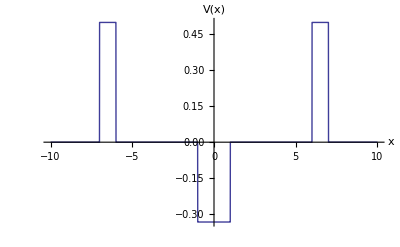
-Graphics-

You will get a warning message from NDSolve. Devise and execute a strategy for deciding if the warning message is serious. If it is, fix the problem.

#### Charge oscillations

A harder but very interesting problem is charge oscillation in multiple quantum wells.  To see charge oscillation you make a multiple quantum well system such as the one shown below. You then make a wave packet that sits in one of the wells. Since the wave packet is not an eigenstate of the total well system (although it may be in an eigenstate one of the wells) the wave packet will oscillate back and forth between the wells. The first experimental work on charge oscillation was done by Loe, Shah, Göbel, Damen, Schmitt-Rink, Schäfer and Köhler [11].
.
Consider the multiple well shown below.  The first step is to create a wave packet which is an eigenstate (or a superposition of several eigenstates) of say the right hand well. Experimentally the wave packet is often a superposition of several states but for simplicity we will start with a wave packets that is in a definite energy eigenstate.

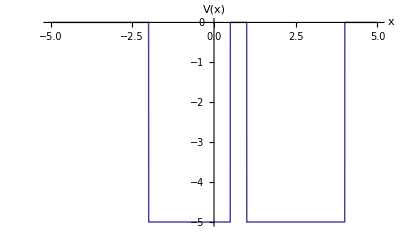

Multiple quantum well structure suitable for observing charge oscillations.

The well shown above is given by

```mathematica
Clear[V]
V[x_]=Piecewise[{{0,x<-2},{-5,-2<x<1/2},{0,1/2<x<1},{-5,1<x<4}}]
```

The first step is to specify the initial wave packet. We want this to be an energy eigenstate of the right-hand well. This well is given by

```mathematica
Clear[VRight]
VRight[x_]=Piecewise[{{0,x<1},{-5,1<x<4}}]
```

```mathematica
Plot[VRight[x],{x,-5,5},Exclusions->None,AxesLabel->{"x","V(x)"}]
```

We can use the numerical code that we developed earlier to find the ground state of this well. Of course since this is a finite square well, we could also find the ground state just by solving a set of transcendental equations (see for example Phillips[4]). However, the purely numerical approach will allow us to easily generalize our method to coupled wells of arbitrary shape. For convenience I have bundled all the code we developed for finding bound states into a single function called EigenSolver. For input the function takes the potential, the range over which you want to find the wave function,  the point at which you want to match the left and right wave functions, and a initial guess for the energy. The function returns the energy,  a plot of the potential with the energy of the bound state drawn as a blue line and a plot of the probability distribution. A tooltip shows the equation for the potential upon mouse over. The wave function is stored as an global variable called "wave function."

```mathematica
Developer`SetSystemOptions["EvaluateNumericalFunctionArgument"->False];
EigenSolver[V_,{q_,qmin_,qmax_},matchPoint_,EnergyGuess_]:=Module[{MatchingPoint,leftψ,rightψ,scaleLeft,scaleRight,DRight,DLeft,result,normalization,plot1,plot2,ψ},
MatchingPoint=Rule[q,matchPoint];
leftψ[ϵ_,q]:=First[NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==ϵ ψ[q],ψ'[qmin]==0.0001,ψ[qmin]==0},ψ[q],{q,qmin,q/.MatchingPoint}]][[1,2]];
rightψ[ϵ_,q]:=First[NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==ϵ ψ[q],ψ'[qmax]==0.0001,ψ[qmax]==0},ψ[q],{q,qmax,q/.MatchingPoint}]][[1,2]];
scaleLeft[ϵ_]:=leftψ[ϵ,q]/.MatchingPoint;
scaleRight[ϵ_]:=rightψ[ϵ,q]/.MatchingPoint;
scaledLeft[ϵ_,q]:=leftψ[ϵ,q]scaleRight[ϵ]/scaleLeft[ϵ];
DRight[ϵ_,q]:=D[rightψ[ϵ,q],q];
DLeft[ϵ_,q]:=D[scaledLeft[ϵ,q],q];
Energy=ϵ/.FindRoot[(DLeft[ϵ,q]/.MatchingPoint)==(DRight[ϵ,q]/.MatchingPoint),{ϵ,EnergyGuess,EnergyGuess+EnergyGuess/10.0}];
result=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==Energy ψ[q],ψ'[qmin]==0.0001,ψ[qmin]==0},ψ[q],{q,qmin,qmax}]];
normalization=1/√NIntegrate[result^2,{q,qmin,qmax}];
wavefunction:=normalization result;
plot1=Show[Plot[Tooltip[V,ToString[TraditionalForm[V]]],{q,qmin,qmax},PlotPoints->100,Exclusions->None,PlotStyle->{RGBColor[1,0,0],Opacity[.5]},AxesOrigin->{qmin,0},AxesLabel->{"x","Energy"}],Graphics[{RGBColor[0,0,1],Line[{{qmin,Energy},{qmax,Energy}}]}]];
plot2=Plot[normalization^2 result^2,{q,qmin,qmax},PlotRange->All,AxesLabel->{"x","Probablity"},RotateLabel->True];
Print[StringJoin["Energy=",ToString[Energy]]];
GraphicsArray[{{plot1},{plot2}}]]
```

We can now run our code on the right-hand well to find the ground state.

```mathematica
EigenSolver[VRight[x],{x,-6,6},1,-4]
```

There is one small complication. The function EigenSolver has returned the wave function only over the interval -6<x<6 but we will want to solve the time-dependent Schrödinger equation over the larger interval since we have two wells. The method used for finding the wave function breaks down if we try to solve on intervals which are too large compared to the extent of the well. You should try this for yourself! However we know that for bound states the wave function must vanish at infinity, so we can define an initial wave by simply setting the wave function to zero ousidet the interval -6<x<6. You should check the value of the wave function at x=6 to convince yourself that this is legitimate.

```mathematica
initialShape=Piecewise[{{0,x<-6},{wavefunction,-6<x<6},{0,x>6}}]
```

We are now ready to solve the time-dependent Schrödinger equation. Just as before we will force the wave function to zero at the ends of a box. The box length should be "large" compared to the region occupied by the wells.

```mathematica
eqn=ⅈ ℏ D[ψ[x,t],t]==-(ℏ^2/2m)D[ψ[x,t],{x,2}]+V[x]ψ[x,t]
```

Trying the standard call to NDSolve (given below) reveals problems. The cell below has been made inactive to prevent you from accidentally evaluating it. You can change this from the Cell menu using the Cell Properties sub-menu. If you evaluate it you will find that the code takes a very long time to run, uses a huge amount of virtual memory and depending on your machine may cause the kernel to quit with an out of memory error.

```mathematica
L=14;
m=1;
ℏ=1;
wavefunction2[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,40},MaxSteps->40000][[1,1,2]];
```

To get a solution we must give NDSolve some help. The default method over-samples in the spatial dimension and thus breaks the PDE up into more ODE's than is necessary. However NDSolve offers the user great control over the method used and the number of points sampled. We can use the Method option to select the method that we want to use. I have chosen the Method of Lines (the only method currently implemented for this type of problem), picked a tensor product grid for the spacial discretization, and most importantly set the spacial grid to 400 points by specifying that the maximum and minimum number of grid points should be 400. I am indebted Rob Knapp of Wolfram Research for help with selecting the best method. You can read about the options available for NDSolve in the advanced documentation for NDSolve.

```mathematica
kernalTime=TimeUsed[];
nx = 400;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[wavefunction]
wavefunction2[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->40000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
TimeUsed[]-kernalTime
```

With this method the code is fairly fast but you notice that we get a warning message about the accuracy.  We will have to check the accuracy of our result but first we will plot the probability distribution. We need the wave function times its complex conjugate.

```mathematica
wave[x_,t_]:=Chop[Times[wavefunction2[x,t],(wavefunction2[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

Plotting this at say t=20gives a result that looks reasonable.

```mathematica
Plot[wave[x,20],{x,-L,L},PlotRange->All]
```

To check the accuracy of the result we can double the number of grid points used by setting MaxPoints and MinPoints to 800. Not surprisingly this doubles the computation time. I have called the result HPwavefunction (for high precision wave function.)

```mathematica
kernalTime=TimeUsed[];
nx = 800;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[wavefunction]
HPwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->40000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
TimeUsed[]-kernalTime
```

We can now form the probability distribution

```mathematica
HPwave[x_,t_]:=Chop[Times[HPwavefunction[x,t],(HPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

and compare the absolute value of the difference between our result with 800 grid points and the result with 400 grid points. The plot below shows the difference at t=10.

```mathematica
Plot[Abs[HPwave[x,10]-wave[x,10]],{x,-L,L},PlotRange->All,PlotLabel->"difference at t=10",AxesLabel->{"x","difference"}]
```

These errors look small but we are faced with the question of what to compare them to. In other word,s small compared to what? We can not compute a percent error by dividing by the probability distribution because the probability distribution is zero at several points. We also have only a snapshot in time. Maybe the errors are worse later. This question is easily answered with an animation in time.

```mathematica
ListAnimate[Table[Plot[Abs[HPwave[x,t]-wave[x,t]],{x,-L,L},PlotRange->{0,0.1},AxesLabel->{"x","difference"}],{t,0,40,1}]]
```

The hard question is small compared to what? We can compare the error to the probability distribution itself.

```mathematica
Plot[{HPwave[x,10],Abs[HPwave[x,10]-wave[x,10]]},{x,-L,L},PlotRange->All,AxesLabel->{"x",None}]
```

The error in the probability distribution is shown in purple. The probability distribution itself is in blue.

This still looks good but what about at other times? If we animate the result

```mathematica
ListAnimate[Table[Plot[{HPwave[x,t],Abs[HPwave[x,t]-wave[x,t]]},{x,-L,L},PlotRange->{0,.6},AxesLabel->{"x",None},PlotLabel->StringJoin["t=",ToString[t]]],{t,0,40,1}]]
```

The error in the probability distribution is shown in purple. The probability distribution itself is in blue.

we see that although the results are good overall, at t=36 the error in the region x<0 is almost as large as the function itself. This should not be too surprising since the overall value of the function is small in that region. When the absolute value of a function is small even a small absolute error is a large relative error. The solution as it stands may well be good enough. It all depends on what you want it for. If you really need a high accuracy solution for all x and t you can always double the number of grid points again. Of course you pay a price in both memory and CPU time. This is done below.

```mathematica
kernalTime=TimeUsed[];
nx =1600;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[wavefunction]
VHPwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->40000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
TimeUsed[]-kernalTime
```

```mathematica
VHPwave[x_,t_]:=Chop[Times[VHPwavefunction[x,t],(VHPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
ListAnimate[Table[Plot[{VHPwave[x,t],Abs[VHPwave[x,t]-HPwave[x,t]]},{x,-L,L},PlotRange->{0,.6},AxesLabel->{"x",None},PlotLabel->StringJoin["t=",ToString[t]]],{t,0,40,1}]]
```

The error in the probability distribution is shown in purple. The error is the absolute value of the difference between using 800 grid points and 1600 grid points.The probability distribution itself is in blue.

Now that we have confidence that we understand the accuracy of our solution, we should plot it and the well structure on the same plot. I have scaled the well by 1/5 for visual clarity.

```mathematica
wavePlot=ListAnimate[Table[Plot[{.2V[x],VHPwave[x,t]},{x,-L,L},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0]},PlotRange->{-1.1,.75},Exclusions->None,AxesLabel->{"x",None}],{t,0,40,1}]]
```

The time dependent probability density is shown in red. The upper y-axis shows the probability of finding the particle. The lower y axis gives the well depth. Well depths are scaled by a factor of 1/5 so -1 on the figure corresponds to -5. The well structure is shown in black.

Looking at the animation we see that probability of finding the particle is always higher in the righ- hand well, but that we get some oscillation into the left-hand well.  If we look at a time when there is a significant probability of finding the wave packet in the left well we see that the distances between the nodes in the left and right wells are the same. Since the energy of the packet is proportional to the distance between the nodes, this tells us that our solution conservers energy which is reassuring.

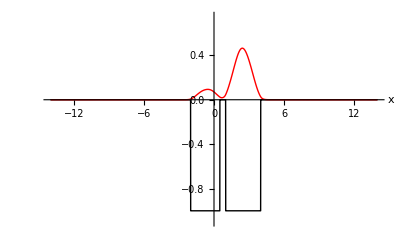

Oscillation into the second well. Note the wavelength of the left peak.

If we make the left well some what deeper we will get more oscillation into the left well.  Suppose we have the following well.

```mathematica
Clear[V]
V[x_]=Piecewise[{{0,x<-2},{-7,-2<x<1/2},{0,1/2<x<1},{-5,1<x<4}}]
```

```mathematica
Plot[V[x],{x,-5,5},Exclusions->None]
```

Since the right hand well is unchanged we can use the same initial shape as before and simply repeat the calculation with the new potential.

```mathematica
nx = 400;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[wavefunction]
wavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->40000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
```

```mathematica
wave[x_,t_]:=Chop[Times[wavefunction[x,t],(wavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
wavePlot=ListAnimate[Table[Plot[{(1/7)V[x],wave[x,t]},{x,-L,L},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0]},PlotRange->{-1.1,.75},Exclusions->None,AxesLabel->{"x",None},PlotLabel->StringJoin["t=",ToString[PaddedForm[t,3]]]],{t,0,40,.5}]]
```

The time dependent probability density is shown in red. The upper y-axis shows the probability of finding the particle. The lower y axis gives the well depth. Well depths are scaled by a factor of 1/7 so -1 on the figure corresponds to -7. The well structure is shown in black.

In experiments what is detected is not the oscillation of the wave packet, but rather the electromagnetic radiation emitted due to the acceleration of the charge density. The experiments [11,12,13] measure the emitted power which is propositional to the square of the acceleration. An accurate calculation of the emitted radiation is a hard problem that is beyond the scope of this module.  However we can see the qualitative features of the radiation by just computing the acceleration of the wave packet. The major flaw in this approach is that it does not take into account the energy the wave packet loses due to the radiation.  The first step is to compute <x>. We can then differentiate the result to get the average acceleration. Since <x> = ∫ψ^*x ψ ⅆx we can compute it with the code below.

```mathematica
integrand[x_,t_]:=Chop[(wavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b]) x  wavefunction[x,t]]
```

Version 6.0 can not do the integral analytically and so we must resort to numerical integration.

```mathematica
Clear[xAverage]
xAverage[t_]:=NIntegrate[integrand[x,t],{x,-14,14}]
```

Plotting the result shows that there maybe a problem.

```mathematica
xAveragePlot=Plot[xAverage[t],{t,0,40},AxesLabel->{"t","<x>"}]
```

The function does not look very smooth and we need to take two time derivatives of it. Taking a derivative always gives a result that is less smooth then the original function. The first  question to ask is our solution accurate enough to give an accurate value for <x>? We can answer this question by computing a  solution with more grid points and comparing the answers.  The solution from which the plot of xAverage was generated was computed using 400 grid points. Let's try 800. I have called the result HPwavefunction (for high precision wave function).

```mathematica
nx =800;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[HPwavefunction]
HPwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->100000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
```

We now form the probability density and the integrand we need to compute <x> just as before. The variables have all been renamed with an HP as the first two letters.

```mathematica
HPwave[x_,t_]:=Chop[Times[HPwavefunction[x,t],(HPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
HPintegrand[x_,t_]:=Chop[(HPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b]) x  HPwavefunction[x,t]]
```

```mathematica
Clear[HPxAverage]
HPxAverage[t_]:=NIntegrate[HPintegrand[x,t],{x,-14,14}]
```

```mathematica
HPxAveragePlot = Plot[HPxAverage[t], {t, 0, 40},PlotStyle->Red,AxesLabel->{"t","<x>"}]
```

```mathematica
Show[HPxAveragePlot,xAveragePlot,PlotLabel->"800 grid points shown in red \n 400 grid points shown in blue",AxesLabel->{"t","<x>"}]
```

The two plots don't look very much alike so we should try using a still finer grid, say 1200 points and 2400 points. Here I have tagged the variable names with VHP (for very-high precision) for the 1200 point grid and UH (for ultra-high precision) for the 2400 point grid. Notice that this example shows that the degree of accuracy needed depends on what we want to do with the data. The two grid spacings will yield  wave packet oscillations that look very much the same but will give significantly different accelerations.

```mathematica
nx = 1200;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[VHPwavefunction]
VHPwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->100000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
```

```mathematica
VHPwave[x_,t_]:=Chop[Times[VHPwavefunction[x,t],(VHPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
VHPintegrand[x_,t_]:=Chop[(VHPwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b]) x  VHPwavefunction[x,t]]
```

```mathematica
Clear[VHPxAverage]
VHPxAverage[t_]:=NIntegrate[VHPintegrand[x,t],{x,-14,14}]
```

```mathematica
VHPxAveragePlot=Plot[VHPxAverage[t],{t,0,40},AxesLabel->{"t","<x>"},PlotStyle->Black]
```

```mathematica
nx = 2400;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[UHwavefunction]
UHwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->100000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
```

```mathematica
UHwave[x_,t_]:=Chop[Times[UHwavefunction[x,t],(UHwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
UPintegrand[x_,t_]:=Chop[(UHwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b]) x  UHwavefunction[x,t]]
```

```mathematica
Clear[UPxAverage]
UPxAverage[t_]:=NIntegrate[UPintegrand[x,t],{x,-14,14}]
```

```mathematica
UPxAveragePlot=Plot[UPxAverage[t],{t,0,40},PlotStyle->Green,AxesLabel->{"t","<x>"}]
```

Comparison of the two plots shows that they are still not quite the same.

```mathematica
Show[UPxAveragePlot,VHPxAveragePlot,PlotLabel->"1200 grid points shown in black \n 2400 grid points shown in green"]
```

If we try a still finer grid say with 3600 grid points we see that we have finely converged. For the 3600 point grid I have tagged the variables with the letters EH (extremely high).

```mathematica
nx = 3600;
tend = 40;
L=14;
m=1;
ℏ=1;
Clear[EHwavefunction]
EHwavefunction[x_,t_]=NDSolve[{eqn,ψ[x,0]==initialShape,ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,tend},MaxSteps->100000,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid", "MinPoints"->nx, "MaxPoints"->nx}}][[1,1,2]];
```

```mathematica
EHwave[x_,t_]:=Chop[Times[EHwavefunction[x,t],(EHwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b])]]
```

```mathematica
EHintegrand[x_,t_]:=Chop[(EHwavefunction[x,t]/.Complex[a_,b_]->Complex[a,-b]) x  EHwavefunction[x,t]]
```

```mathematica
Clear[EHxAverage]
EHxAverage[t_]:=NIntegrate[EHintegrand[x,t],{x,-14,14}]
```

```mathematica
EHPxAveragePlot=Plot[EHxAverage[t],{t,0,40},AxesLabel->{"t","<x>"},PlotStyle->Purple]
```

```mathematica
Show[UPxAveragePlot,EHPxAveragePlot,PlotLabel->" 2400 grid points shown in green,\n 3600 grid points shown in purple"]
```

Notice that the two plots overlay one another.  Since we now have confidence in our 2400 grid point result we can, and should, use it rather than the more computationaly intensive 3600 grid point result. Although the overall shape of the curve is fine you can see that there is some jitter and this will defeat an attempt to directly take a derivative. We could data smooth but we can also sample the curve and then fit a function to it.

The trick is to fit <x> to a smooth function and then differentiate the result. The question is how to fit xAverage. If we look at the plot xAverage, a polynomial fit does not look promising. However we could try fitting it with a sum of cosine functions. In fact Fourier analysis [14] guarantees that this will work.
The first step is to sample the function.

```mathematica
data=Table[{t,UPxAverage[t]},{t,0.,40.,.5}];
```

```mathematica
dataPlot=ListPlot[data,PlotStyle->Red]
```

Comparing this to the plot of the function shows that we have accurately recreated the function.

```mathematica
Show[dataPlot,UPxAveragePlot]
```

We want to fit the sampled points with a function of the form

f(t)=∑_(n=0)^N a(n)  cos (n π t/40)

where N+1 is the number of terms. Note that the argument to the cosine is n π t/40. The reason for the factor of 40 is that we are interested in the interval [0,40] and on this interval t/40 runs from zero to one. Once we have our function we can use FindFit to find the coefficients a(n). How many terms should we take? There is no easy way to know this ahead of time. It's best just to try it and see if you get a good fit. The module below shows what happens as we increase the number of terms.

```mathematica
Clear[fit]
fit[terms_]:=Module[{},
model=Sum[a[n] Cos[n π t/40],{n,0,terms}];
par=Table[a[n],{n,0,terms}];
results=Chop[FindFit[data,model,par,t]];
resultPlot=Plot[model/.results,{t,0,40},PlotLabel->StringJoin["number of terms=",ToString[terms+1]]];
Show[resultPlot,ListPlot[data,PlotStyle->Red],PlotRange->{{0,40},{1.6,2.5}}]]
```

```mathematica
Manipulate[fit[n],{n,1,30,1},SaveDefinitions->True]
```

From the interactive graphic it looks like an upper limit of N=30 does an excellent job of fitting the data.

```mathematica
terms=30;
model=Sum[a[n] Cos[n π t/40],{n,0,terms}];
par=Table[a[n],{n,0,terms}];
results=Chop[FindFit[data,model,par,t]]
```

It is now easy to take the second derivative of <x> with respect to time and plot the resulting acceleration.

```mathematica
aBar=D[(model/.results),{t,2}];
```

```mathematica
newabarPlot=Plot[aBar,{t,0,40},AxesLabel->{"t","a"},PlotStyle->Red]
```

You should of course be deeply suspicious of the result at t=40 which is an artifact of the Fourier fit. The power emitted by a moving charge is given for the non-relativistic case by Larmor's formula [15] and is P=(2 e^2)/(3 c^3)(|a|)^2.  So the power is proportional to the square of the acceleration.

```mathematica
Plot[aBar^2, {t, 0, 39}, AxesLabel -> {"t", "a^2"}, PlotStyle -> Red,PlotRange->All,PlotLabel->"Power as a function of time"]
```

Data for the radiation emitted in charge oscillations is given in [12,13]. The exact shape of the signal depends strongly on the experimental set-up.  The signal dies off quickly in the experimental data due to energy loss from the emitted radiation. This effect is not modeled by our code.

#### Wave packet splitting

An interesting wave packet phenomena of current interest is wave packet splitting. A simple method for splitting a wave packet was recently proposed by Zhang et. al. [16]. Wave packet splitting using a double well has recently been experimentally realized by Hall et. al.  [17] . We can fairly easily numerically simulate wave packet splitting.

We first define a static potential.

```mathematica
Subscript[V, 1][x_]:=Subscript[V, 0] Exp[-3 x^2]
Subscript[V, 0]=-5;
```

```mathematica
Plot[Subscript[V, 1][x],{x,-5,5},PlotRange->All,AxesLabel->{"x","V_1(x)"}]
```

We now define a second potential which is time-dependent. This potential is left moving and its speed is controlled by ω. At t=0 the potential is centered around x=5 so that the two potentials are distinct at t=0.

```mathematica
Subscript[V, 2][x_,t_]:= Subscript[V, 0] Exp[-3(x-5 +ω t)^2]
```

The full potential is V_1+V_2 which I have plotted below for ω=1.

```mathematica
ω=1;
ListAnimate[Table[Plot[Subscript[V, 1][x]+Subscript[V, 2][x,t],{x,-10,10},PlotRange->{0,-10},AxesLabel->{"x","V_total(x)"}],{t,0,10,0.5}]]
```

We start our wave packet in an eigenstate of V_1, the stationary well. To find the eigenstates we use the module EigenSolver which we have used before. The code is repeated below for convenience.

```mathematica
Developer`SetSystemOptions["EvaluateNumericalFunctionArgument"->False];
EigenSolver[V_,{q_,qmin_,qmax_},matchPoint_,EnergyGuess_]:=Module[{},
MatchingPoint=Rule[q,matchPoint];
leftψ[ϵ_,q]:=First[NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==ϵ ψ[q],ψ'[qmin]==0.0001,ψ[qmin]==0},ψ[q],{q,qmin,q/.MatchingPoint}]][[1,2]];
rightψ[ϵ_,q]:=First[NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==ϵ ψ[q],ψ'[qmax]==0.0001,ψ[qmax]==0},ψ[q],{q,qmax,q/.MatchingPoint}]][[1,2]];
scaleLeft[ϵ_]:=leftψ[ϵ,q]/.MatchingPoint;
scaleRight[ϵ_]:=rightψ[ϵ,q]/.MatchingPoint;
scaledLeft[ϵ_,q]:=leftψ[ϵ,q]scaleRight[ϵ]/scaleLeft[ϵ];
DRight[ϵ_,q]:=D[rightψ[ϵ,q],q];
DLeft[ϵ_,q]:=D[scaledLeft[ϵ,q],q];
Energy=ϵ/.FindRoot[(DLeft[ϵ,q]/.MatchingPoint)==(DRight[ϵ,q]/.MatchingPoint),{ϵ,EnergyGuess,EnergyGuess+EnergyGuess/10.0}];
result=First[ψ[q]/.NDSolve[{-D[ψ[q],{q,2}]+V ψ[q]==Energy ψ[q],ψ'[qmin]==0.0001,ψ[qmin]==0},ψ[q],{q,qmin,qmax}]];
normalization=1/√NIntegrate[result^2,{q,qmin,qmax}];
plot1=Show[Plot[Tooltip[V,ToString[TraditionalForm[V]]],{q,qmin,qmax},PlotPoints->100,PlotRange->All,PlotStyle->{RGBColor[1,0,0],Opacity[.5]},AxesOrigin->{qmin,0},AxesLabel->"Energy"],Graphics[{RGBColor[0,0,1],Line[{{qmin,Energy},{qmax,Energy}}]}]];
plot2=Plot[normalization^2 result^2,{q,qmin,qmax},PlotRange->All,AxesLabel->{None,"Probablity"},RotateLabel->True];
Print[StringJoin["Energy=",ToString[Energy]]];
GraphicsArray[{{plot1},{plot2}},GraphicsSpacing->-1]]
```

Using EigenSolver we can easily find the ground state. The wave function is returned as the variable normalization result.

```mathematica
EigenSolver[Subscript[V, 1][x],{x,-5,5},1,-4.5]
```

Once again we need the wave function over a larger interval than is returned by EigenSolver, but the value of the wave function is so small outside of the interval -5<x<5 that we can just set it to zero.

```mathematica
Subscript[ψ, initial][x_]=Piecewise[{{0,x<-5},{normalization result,-5≤x≤5},{0,x>5}}]
```

The initial wave function is plotted below.

```mathematica
Plot[Subscript[ψ, initial][x],{x,-10,10},PlotRange->All,AxesLabel->{"x",Subscript[ψ, initial]}]
```

Now that we have the initial wave function we can solve the wave equation with the full time-dependent potential.

```mathematica
Clear[ℏ,m,ψ,V]
eqn=ⅈ ℏ D[ψ[x,t],t]==-(ℏ^2/2m)D[ψ[x,t],{x,2}]+V[x,t]ψ[x,t]
```

As usual we will solve the equation in a box and force the wave function to zero at the box boundaries.  The box runs from -L to L and I have taken L=8 in units in which m=1 and ℏ=1.

```mathematica
m=1;
ℏ=1;
L=8;
V[x_,t_]:=Subscript[V, 1][x]+Subscript[V, 2][x,t]
```

Since we don't want the wave packet to hit the boundaries of the box I have tracked the solution only until t=8. I have also used AccuracyGoal → 2. This gives a low accuracy solution (the default to AccuracyGoal → 6) but it's fast and does not take much memory.  We will have to check to see if our low accuracy solution is good enough.

```mathematica
Clear[packet]
packet[x_,t_]=NDSolve[{eqn,ψ[x,0]==Subscript[ψ, initial][x],ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,10},MaxSteps->100000,AccuracyGoal->2][[1,1,2]]//Timing
```

We can now form the wave packet

```mathematica
wave[x_,t_]:=Chop[Times[packet[x,t][[2]],Conjugate[packet[x,t][[2]]]]]
```

and plot the time evolution.

```mathematica
ListAnimate[Table[Plot[Evaluate[{V[x,t]/10,wave[x,t]}],{x,-L,L},PlotRange->{-1,1.2},PlotLabel->"ω=1",PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]},AxesLabel->{"x","P(x,t)"}],{t,0,10,.1}]]
```

Wave packet splitting. The wave packet is shown in black. The potential is shown in red.

It is important to understanding what the animation really means. Remember that we are looking at a probability distribution so we don't split the wave packet. We split the probability distribution. There is a chance that the wave packet stays in the stationary well and a chance that it moves off with the moving potential. Notice that for our potential, the probability of moving the wave packet is not very high.

To check the accuracy of our solution we can re-solve the equation with an accuracy goal of 3 and compare the solutions.

```mathematica
Clear[HPpacket]
HPpacket[x_,t_]=NDSolve[{eqn,ψ[x,0]==Subscript[ψ, initial][x],ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,10},MaxSteps->100000,AccuracyGoal->3][[1,1,2]]//Timing
```

```mathematica
HPwave[x_,t_]:=Chop[Times[HPpacket[x,t][[2]],Conjugate[HPpacket[x,t][[2]]]]]
```

Plotting shows that the two solutions are very similar. You can barely see the difference between the two curves.

```mathematica
ListAnimate[Table[Plot[Evaluate[{V[x,t]/10,HPwave[x,t],wave[x,t]}],{x,-L,L},PlotRange->{-1,1.2},PlotLabel->"ω=1",PlotStyle->{Black,Red,Blue},AxesLabel->{"x","P(x,t)"}],{t,0,10,.1}]]
```

Comparing our two solutions. The two wave packet solutions are shown in red (AccuracyGoal→3) and blue (AccuracyGoal→2). Note that there is little difference between them. The potential is shown in black.

Another way to split a wave packet into two is to start from a single well and split it into two wells. This has not yet been done experimentally but it allows you to split the packet with equal probability.  Suppose we have the following potential

```mathematica
V[x_,t_]:= (Subscript[V, 0]/2) Exp[-3(x +ω t)^2]+(Subscript[V, 0]/2) Exp[-3(x -ω t)^2]
```

This potential is centered at x=0  at t=0 and is composed of equal parts of a left moving and right moving wave. The potential's time-dependence is plotted below for V_0=-5 and ω=1.

```mathematica
ω=1;
Subscript[V, 0]=-5;
ListAnimate[Table[Plot[V[x,t],{x,-10,10},PlotRange->{0,-6},AxesLabel->{"x","V_total(x)"}],{t,0,10,0.5}]]
```

Notice that at t=0 the potential is the same as our original static potential so that we can use the same initial wave shape. This makes it easy to re-solve the wave equation.

```mathematica
Clear[packet]
packet[x_,t_]=NDSolve[{eqn,ψ[x,0]==Subscript[ψ, initial][x],ψ[-L,t]==0,ψ[L,t]==0},ψ[x,t],{x,-L,L},{t,0,10},MaxSteps->100000,AccuracyGoal->2][[1,1,2]]//Timing
```

We now form the probability density

```mathematica
wave[x_,t_]:=Chop[Times[packet[x,t][[2]],Conjugate[packet[x,t][[2]]]]]
```

and plot the result. To avoid effects from the box boundary we plot only until t=5.

```mathematica
ListAnimate[Table[Plot[Evaluate[{V[x,t]/10,wave[x,t]}],{x,-L,L},PlotRange->{-1,1.2},PlotLabel->"ω=1",PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]},AxesLabel->{"x","P(x,t)"}],{t,0,5,.1}]]
```

Wave packet splitting with equal probabilities. The wave packet is shown in black. The potential is shown in red.

Notice that we get equal probabilities of moving the wave packet to the right or the left.

## Projects

#### Charge Oscillations

In real experiments the initial state of the wave packet is not a single energy eigenstate but rather a mixture of eigenstates. Investigate what happens when you start the system in a mixture of eigenstates of the right-hand well. Look up the experimental papers [11,12,13] so that you start with realistic well parameters.

#### Wave Packet Splitting

Make a quantum tram. Your tram (moving wave packet) should pick-up a passenger (wave packet) with some probability P_1 and drop them off at second station (well) with a second probability P_2. Investigate how P_1 and P_2 depend on the speed of your tram and the width and depth of your wells.

## References

[1]	R. Dingle, W. Wiegmann, and C. H. Henry, PRL. 33, 827 (1974)
[2]	Claude Weisburch and Borge Vinter, Quantum  Semiconductor Structures, Academic Press,  		San 	Diego, 1991.
[3]	Stephen Thornton and  Andrew Rex, Modern Physics, Third Edition, Thompson,  Beaumont, 		2006.
[4]	A. C. Phillips, Introduction to Quantum Mechanics, Wile, Catchiest, 2003.
[5]	Gerald Bastard, Wave Mechanics Applied to Semiconductor Heterostructures, Halted Press, 			New 	York 1988
[6]	Herald Iback and Hans Lüth, Solid-State Physics, Second Edition, pages 384-388, Springer, 				Berlin, 1995.
[7]	Press, Flannery, Teukolsky, and Vetterling, Numerical Recipes in C, Second Edition, page 710, 			Cambridge Press, Cambridge, England, 1992.
[8]	Roman Maeder, Programming in Mathematica, Third Edition, page 208, Addison Wesley,  				Reading Massachusetts, 1997.
[9]	Tao Pang, Computational Physics, page 79,  Cambridge Press, Cambridge England, 1997.
[10]	Abraham  Goldberg, Harry M. Schey and Judo Schwartz, Am. J. Phys. 35, 177 (1967).
[11]	Karl Leo, Jagdeep Shah, Ernst O. Göbel, Theodore C. Damen, Stefan Schmitt-Rink, Wilfried Schäfer and Klaus Köhler, PRL, 66, 201 (1991).
[12]	Hartmut G. Roskos, Martin C. Nuss, Jagdeep Shah, Karl Leo, David A. B. Miller, A. Mark Fox,  Stefan Schmitt-Rinkand Klaus Köhler, PRL 68, 2216 (1992).
[13]	A. Bonvalet, J. Nagle, V. Berger, A. Migus, J.-L. Martin and M. Joffre, PRL 76, 4392, (1996).

[14]	See for example George Arfkin and Hans Weber, Mathematical Methods for Physicists,

Academic Press; 6 edition, (2005).

[15]	See for example, J. D. Jackson, Classical Electrodynamics,  third edition, Wiley,  (1998).
[16]	M. Zhang, P. Zhang. M.S. Chapman and L. You, PRL 97, 070403 (2006).
[17]	B. V. Hall, S. Whitlock, R. Anderson, P. Hannaford and A. I.  Sidorov, PRL 98, 030402 (2007).